# PRACTICAL 1 : Introduction to Mathematica

## ARITHMETIC OPERATIONS

## -- Addition (+) ; Plus[a,b] = a+b

```mathematica
23+45
```

68

```mathematica
Plus[4+45]
```

49

## -- Subtraction (-) ; Subtract[a,b] = a-b

```mathematica
23-4
```

19

```mathematica
34.54-23.123
```

11.417

```mathematica
-345+231-123
```

-237

```mathematica
Subtract[34,6]
```

28

## -- Multiplication (*) ; Times[a,b] = a*b

```mathematica
23*4
```

92

```mathematica
-23*2
```

-46

```mathematica
Times[2,5]
```

10

```mathematica
Times[5.5,3]
```

16.5

## -- Division (/) ; Divide[a,b] = a/b ; a./b. (for decimal type)

```mathematica
23/4
```

23/4

```mathematica
23./4.
```

5.75

```mathematica
Divide[55,4]
```

55/4

```mathematica
N[23/4]
```

5.75

## -- Power (^)

```mathematica
2^4
```

16

```mathematica
3.4^2
```

11.56

## OPERATIONS WITH UNDEFINED VARIABLES

```mathematica
2*B
```

2 B

```mathematica
A*B
```

A B

```mathematica
B 3
```

3 B

```mathematica
A B
```

A B

```mathematica
2 3
```

6

## DECIMAL REPRESENTATION & BASIC FUNCTIONS

## -- Pi

```mathematica
Pi
```

π

## -- N[] (for conversion into decimal representation)

```mathematica
N[Pi]
```

3.14159

```mathematica
Sqrt[5]
```

√5

```mathematica
Sqrt[344]
```

2 √86

```mathematica
N[Sqrt[344]]
```

18.5472

```mathematica
N[%%]
```

2.23607

```mathematica
N[%]
```

2.23607

## -- BASIC FUNCTIONS

```mathematica
Sqrt[34]
```

√34

```mathematica
Sqrt[36]
```

6

```mathematica
Abs[23.4]
```

23.4

```mathematica
Abs[-23.4]
```

23.4

```mathematica
Floor[2.2]
```

2

```mathematica
Floor[2.8]
```

2

```mathematica
Ceiling[2.2]
```

3

```mathematica
Ceiling[2.8]
```

3

```mathematica
N[Sin[30]]
```

-0.988032

```mathematica
ArcSin[1]
```

π/2

```mathematica
Exp[3]
```

ⅇ^3

```mathematica
Log[2]
```

Log[2]

```mathematica
Log[1]
```

0

```mathematica
Log10[2.1]
```

0.322219

## -- List & List operations : Store collection of Data in the list

```mathematica
num={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
fruits={"apple", "mango", "banana"}
```

{apple,mango,banana}

```mathematica
2*num
```

{2,4,6,8,10}

```mathematica
2*fruits
```

{2 apple,2 mango,2 banana}

## -- Range : Produce a list of numbers in different ways

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[2,7]
```

{2,3,4,5,6,7}

```mathematica
Range[2,100,5]
```

{2,7,12,17,22,27,32,37,42,47,52,57,62,67,72,77,82,87,92,97}

## -- Table : Generate value of a list with functions

```mathematica
Table[i^2, {i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[i,{i,5,20}]
```

{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Table[{i^2, i^3},{i,5,10}]//TableForm
```

25 | 125
36 | 216
49 | 343
64 | 512
81 | 729
100 | 1000

## -- TableForm : Generates the values from Table[] into a vertical list form

```mathematica
Table[i^2,{i, 10}]//TableForm
```

1
4
9
16
25
36
49
64
81
100

## -- MatrixForm : Generates the value in the matrix form from the linear form

```mathematica
m={2,4,6,8,10}
```

{2,4,6,8,10}

```mathematica
m//MatrixForm
```

(2
4
6
8
10)

```mathematica
m2={{1,2,3,4,5},{11,22,33,44,55}}
```

{{1,2,3,4,5},{11,22,33,44,55}}

```mathematica
m2//MatrixForm
```

(1 | 2 | 3 | 4 | 5
11 | 22 | 33 | 44 | 55)

```mathematica
2*m
```

{4,8,12,16,20}

```mathematica
m.m2
```

Dot::dotsh: Tensors {2,4,6,8,10} and {{1,2,3,4,5},{11,22,33,44,55}} have incompatible shapes.

{2,4,6,8,10}.{{1,2,3,4,5},{11,22,33,44,55}}

```mathematica
m2[[2,2]]
```

22

```mathematica
m[[1,1]]
```

Part::partd: Part specification {2,4,6,8,10}⟦1,1⟧ is longer than depth of object.

{2,4,6,8,10}⟦1,1⟧

## -- Replacement Operator (/.) : Used to replace the variable with other variables or expressions

```mathematica
x+y+6
```

6+x+y

```mathematica
x+y+6 /.{x->4, y->5}
```

15

## -- Clearing Variables : Removes all/any variable definitions ( Clear[a] ; ClearAll )

```mathematica
Clear[x]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Clear[x,y]
```

```mathematica
sample=100
```

100

```mathematica
clear[sample]
```

clear[100]

```mathematica
sample
```

100

## -- //Expand and Simplify[]

```mathematica
ex1=(x+3)^2-5
```

-5+(3+x)^2

```mathematica
(x+3)^2-5//Expand
```

4+6 x+x^2

```mathematica
(x+2)^3-3//Expand
```

5+12 x+6 x^2+x^3

```mathematica
Simplify[ex1]
```

```mathematica
4+6 x+x^2
```

```mathematica
N[Simplify[ex1]]
```

4.+6. x+x^2

```mathematica
FullSimplify[4.+6. x+x^2]
```

4.+x (6.+x)

## USER DEFINED FUNCTIONS

## A function is defined using f[x_]:= x^2 (any expression of x) , where f is the function, x_ is the pattern

```mathematica
f[z_]:=z^2
```

```mathematica
f[3]
```

9

```mathematica
f[3.5]
```

12.25

```mathematica
f[a+b-c]
```

(a+b-c)^2

```mathematica
g[x_, y_] := Sqrt[x2 + y2]
```

```mathematica
g[3,5]
```

g[3,5]

```mathematica
g[4, 3]
```

g[4,3]

```mathematica
fn[a_]:= a^2
```

```mathematica
Expand[fn[3x+5x^2-10]]
```

100-60 x-91 x^2+30 x^3+25 x^4

```mathematica
Expand[Product[x+i, {i,2}]]
```

2+3 x+x^2

## Graphing



```mathematica
f[x_]:=x^3
Plot[x^2, {x,-2,2}]
```

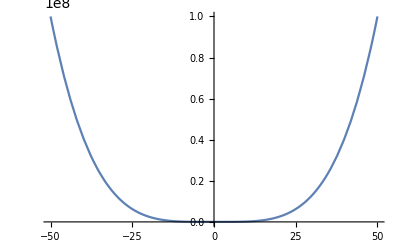

```mathematica
h[x_]:=(x*2)^4
Plot[(x*2)^4, {x,-50,50}]
```